## Exercises: measures of association between two variables

#### 1. A newspaper asks two of its staff to review the coffee quality at different trendy cafés. The coffee can be rated on a scale from 1 (miserable) to 10 (excellent). The results of the two coffee enthusiasts X and Y are as follows:

#### (a) Calculate and interpret Spearman’s rank correlation coefficient with pen and paper and then check your results using Mathematica. (b) Does Spearman’s R differ depending on whether ranks are assigned in a decreasing or increasing order? (c) Suppose the coffee can only be rated as either good (>5) or bad (≤5). Do the chances of a good rating differ between the two journalists?

Solution to (a) :

This indicates a moderate to strong correlation between the ratings of reviewer X and reviewer Y.

```mathematica
cafe={{3,6},{8,7},{7,10},{9,8},{5,4}}
```

{{3,6},{8,7},{7,10},{9,8},{5,4}}

```mathematica
N[SpearmanRho[cafe[[All,1]],cafe[[All,2]]]]
```

0.6

Solution to (b):
R does not differ: using a decreasing order for the ranks, we obtain:
-Graphics-

The sum of d_i^2 =8, as before, and hence, the result for R is the same.

Solution to (c):
We can summarise the results in the following table:

Hence, the odds ratio is equal to OR=(2x4)/(3x1)=8/3=2.66. Hence, it means that the chance of rating a coffee as bad is 2.66 higher for the journalist X compared to journalist Y.

#### 2. We are interested in the pizza delivery data previously discussed. (a) Read in the data and create two new binary variables which describe whether a pizza was hot (>65 ◦C) and the delivery time was short (<30 min). Create a contingency table for the two new variables. (b) Calculate and interpret the odds ratio for the contingency table from (a). (c) Use Cramer’s V and a stacked bar chart to explore the association between the categorical time and temperature variables. (d) Draw a scatter plot for the continuous time and temperature variables. Determine both the Bravais–Pearson and Spearman correlation coefficients. (e) Use methods of your choice to explore the relationship between temperature and driver, operator, number of ordered pizzas and bill. Is it clear which of the variables influence the pizza temperature?

(a) Read in the data and create two new binary variables which describe whether
a pizza was hot (>65 ◦C) and the delivery time was short (<30 min). Create a
contingency table for the two new variables.
Solution to (a):

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pizza=Import["pizza_delivery.csv"]
```

```mathematica
shortcold=Length[Select[pizza[[2;;]],#[[3]]<30&&#[[7]]<=65&]]
```

101

```mathematica
shorthot=Length[Select[pizza[[2;;]],#[[3]]<30&&#[[7]]>65&]]
```

213

```mathematica
longcold=Length[Select[pizza[[2;;]],#[[3]]>=30 && #[[7]]<=65&]]
```

691

```mathematica
longhot=Length[Select[pizza[[2;;]],#[[3]]>=30 && #[[7]]>65&]]
```

261

```mathematica
conttable={{"cold temp.",shortcold,longcold,shortcold+longcold},{"hot temp.",shorthot,longhot,shorthot+longhot},{"sum",shortcold+shorthot,longcold+longhot,shortcold+shorthot+longcold+longhot}}
```

{{cold temp.,101,691,792},{hot temp.,213,261,474},{sum,314,952,1266}}

```mathematica
{{"cold temp.",101,691,792},{"hot temp.",213,261,474},{"sum",314,952,1266}}
```

{{cold temp.,101,691,792},{hot temp.,213,261,474},{sum,314,952,1266}}

```mathematica
Join[{{"","short time","long time","sum"}},conttable]//TableForm
```

| short time | long time | sum
cold temp. | 101 | 691 | 792
hot temp. | 213 | 261 | 474
sum | 314 | 952 | 1266

(b) Calculate and interpret the odds ratio for the contingency table from (a).
Solution to (b):
The odds ratio is OR=(101x261)/(213x691)=0.18 approximately, which means that the chances of receiving a cold pizza are 0.18 times lower if the delivery time is short.

```mathematica
OR=N[(shortcold*longhot)/(shorthot*longcold)]
```

0.179104

(c) Use Cramer’s V and a stacked bar chart to explore the association between the categorical time and temperature variables.
Solution to (c):

```mathematica
conttable2={{shortcold,longcold,shortcold+longcold},{shorthot,longhot,shorthot+longhot},{shortcold+shorthot,longcold+longhot,shortcold+shorthot+longcold+longhot}}
```

{{101,691,792},{213,261,474},{314,952,1266}}

The expected frequencies under the independence assumption are as follows:

```mathematica
n11=N[conttable2[[1,3]]*conttable2[[3,1]]/conttable2[[3,3]]]
```

196.436

```mathematica
n12=N[conttable2[[1,3]]*conttable2[[3,2]]/conttable2[[3,3]]]
```

595.564

```mathematica
n21=N[conttable2[[2,3]]*conttable2[[3,1]]/conttable2[[3,3]]]
```

117.564

```mathematica
n22=N[conttable2[[2,3]]*conttable2[[3,2]]/conttable2[[3,3]]]
```

356.436

```mathematica
expfreq={{n11,n12},{n21,n22}}
```

{{196.436,595.564},{117.564,356.436}}

```mathematica
chimatrix=Table[(conttable2[[i,j]]-expfreq[[i,j]])^2/expfreq[[i,j]],{i,1,2},{j,1,2}]
```

{{46.3664,15.2931},{77.473,25.5531}}

```mathematica
Total[chimatrix,2]
```

164.686

```mathematica
cramerv=Sqrt[Total[chimatrix,2]/(conttable2[[3,3]]*(2-1))]
```

0.360671

We could interpret this as moderate-to-weak relationship between temperature and delivery time.

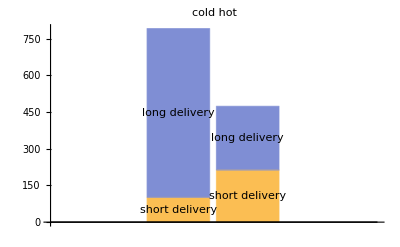

```mathematica
BarChart[{conttable2[[1,1;;2]],conttable2[[2,1;;2]]},ChartLabels->{"short delivery","long delivery" },ChartLayout->"Stacked",PlotLabel->"cold       hot"]
```

(d) Draw a scatter plot for the continuous time and temperature variables. Determine both the Bravais–Pearson and Spearman correlation coefficients.
Solution to (d):

```mathematica
deltime=pizza[[2;;,3]];
```

```mathematica
temp=pizza[[2;;,7]];
```

```mathematica
set=Transpose[{deltime,temp}];
```

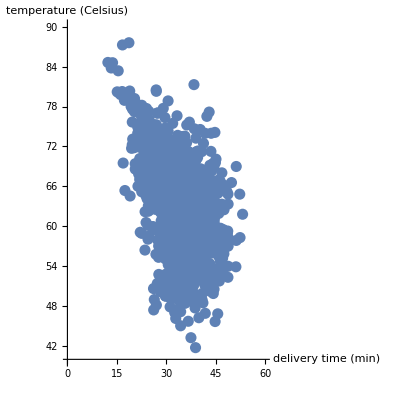

```mathematica
ListPlot[set,AxesLabel->{"delivery time (min)","temperature (Celsius)"},PlotRange->{{0,60},{40,90}},AspectRatio->1,LabelStyle->{FontSize->14},PlotStyle->PointSize[0.02]]
```

```mathematica
Correlation[set[[;;,1]],set[[;;,2]]]
```

-0.433935

```mathematica
SpearmanRho[set[[;;,1]],set[[;;,2]]]
```

-0.39128

The Bravais-Spearman correlation coefficient is -0.43, and the Spearman correlation coefficient is -0.39. They indicate that we have a weak-moderate negative association (decreasing temperature for increasing delivery time).

Solution to (e):
(e) Use methods of your choice to explore the relationship between temperature and driver, operator, number of ordered pizzas and bill. Is it clear which of the variables influence the pizza temperature?
Association between temperature and driver:

Temperature and Driver relationship:

```mathematica
Union[pizza[[2;;,6]]]
```

{Bruno,Domenico,Luigi,Mario,Salvatore}

```mathematica
brunotemp=Select[pizza, #[[6]]=="Bruno"&][[2;;,7]];
```

```mathematica
domenicotemp=Select[pizza, #[[6]]=="Domenico"&][[2;;,7]];
```

```mathematica
luigitemp=Select[pizza, #[[6]]=="Luigi"&][[2;;,7]];
```

```mathematica
mariotemp=Select[pizza, #[[6]]=="Mario"&][[2;;,7]];
```

```mathematica
salvatoretemp=Select[pizza, #[[6]]=="Salvatore"&][[2;;,7]];
```

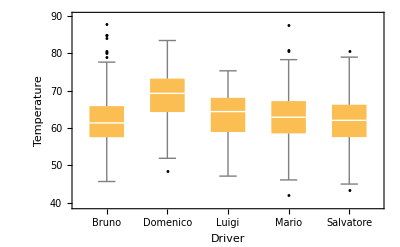

```mathematica
BoxWhiskerChart[{brunotemp,domenicotemp,luigitemp,mariotemp,salvatoretemp},"Outliers",ChartLabels->{"Bruno","Domenico","Luigi","Mario","Salvatore"},FrameLabel->{"Driver","Temperature"},LabelStyle->{FontSize->14}]
```

Dominico seems to deliver pizzas with the highest temperature on average, and Bruno has the lowest median temperature. However, the temperatures of Bruno have several outliers, and the maximum temperature in the entire dataset was delivered by Bruno.

Association between temperature and operator:

```mathematica
Union[pizza[[2;;,4]]]
```

{Laura,Melissa}

```mathematica
laura=Select[pizza,#[[4]]=="Laura"&][[2;;,7]];
```

```mathematica
melissa=Select[pizza,#[[4]]=="Melissa"&][[2;;,7]];
```

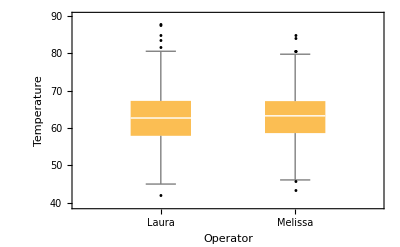

```mathematica
BoxWhiskerChart[{laura,melissa},"Outliers",ChartLabels->{"Laura","Melissa"},FrameLabel->{"Operator","Temperature"},LabelStyle->{FontSize->14}]
```

The temperature seems to be very similar between both operators.

Association between temperature and number of pizzas ordered:

```mathematica
Correlation[pizza[[2;;,7]],pizza[[2;;,9]]]
```

-0.36858

```mathematica
SpearmanRho[pizza[[2;;,7]],pizza[[2;;,9]]]
```

-0.392063

Higher number of pizzas is weak-moderately negatively associated with lower temperatures of pizza on arrival.

Association between temperature and bill:

```mathematica
Correlation[pizza[[2;;,7]],pizza[[2;;,8]]]
```

-0.415156

```mathematica
SpearmanRho[pizza[[2;;,7]],pizza[[2;;,8]]]
```

-0.370781

Higher bills are moderately negatively associated with lower temperature of pizzas on arrival.